# DQPTs 2026

```mathematica
SetDirectory[NotebookDirectory[]];
```

## Figure 1

### Top panel

```mathematica
r=10;
dataneg=Import["Data/negativities_Quench1_R50.dat"];
datRateg=Table[{dataneg[[i,1]],-(1/r)*Log[Abs[dataneg[[i,6]]-dataneg[[i,7]]]]},{i,1,Length[dataneg]}] ;
datIm=Table[{dataneg[[i,1]],dataneg[[i,7]]},{i,1,Length[dataneg]}] ;
datIp=Table[{dataneg[[i,1]],dataneg[[i,6]]},{i,1,Length[dataneg]}] ;
datGg=Table[{dataneg[[i,1]],-(1/r)*Log[Abs[1-dataneg[[i,7]]/dataneg[[i,6]]]]},{i,1,Length[dataneg]}] ;
datnegg=Table[{dataneg[[i,1]],dataneg[[i,2]]},{i,1,Length[dataneg]}] ;
datnegl=Table[{dataneg[[i,1]],dataneg[[i,3]]},{i,1,Length[dataneg]}] ;
datWming=Table[{dataneg[[i,1]],Abs[dataneg[[i,4]]]},{i,1,Length[dataneg]}] ;
datWminl=Table[{dataneg[[i,1]],Abs[dataneg[[i,5]]]},{i,1,Length[dataneg]}] ;
dataneg2=Import["Data/negativities_Quench1_R50.dat"];
datRateg2=Table[{dataneg2[[i,1]],-(1/r)*Log[Abs[dataneg2[[i,6]]-dataneg2[[i,7]]]]},{i,1,Length[dataneg2]}] ;
datGg2=Table[{dataneg2[[i,1]],-(1/r)*Log[Abs[1-dataneg2[[i,7]]/dataneg2[[i,6]]]]},{i,1,Length[dataneg2]}] ;
datnegg2=Table[{dataneg2[[i,1]],dataneg2[[i,2]]},{i,1,Length[dataneg2]}] ;
datWming2=Table[{dataneg2[[i,1]],Abs[dataneg2[[i,4]]]},{i,1,Length[dataneg2]}] ;
```

```mathematica
Show[ListPlot[{datRateg},PlotStyle->{{Red,Thickness[0.004]},{Gray,Thickness[0.004]},{Gray,Thickness[0.004]}},Joined->True,GridLines->{{6.0},{}},FrameTicks->{{{0,0.2,0.4,0.6,0.8,1},{None}},{{0,2,4,6,8,10},{None}}},PlotLegends->Placed[{},{0.09,0.75}],GridLinesStyle->{{Black},{}},PlotRange->{{0,10},{-0.001,0.55}},Frame->True,LabelStyle->{18,Black}]]
```

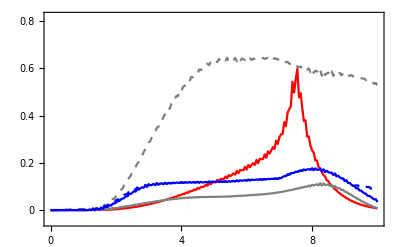

```mathematica
Show[ListPlot[{datnegg},PlotStyle->{{Gray,Dashed}},Joined->True,GridLines->{{},{}},FrameTicks->{{{0,0.2,0.4,0.6,0.8,1},{None}},{{0,2,4,6,8,10},{None}}},GridLinesStyle->{{Black},{}},PlotLegends->Placed[{""},{0.09,0.9}],PlotRange->{{0,10},{-0.05,0.82}},Frame->True,LabelStyle->{18,Black}],ListPlot[datWming,Joined->True,PlotStyle->{{Blue,Dashed}},PlotLegends->Placed[{""},{0.09,0.65}]],ListPlot[datGg,Joined->True,PlotStyle->{{Red}},PlotLegends->Placed[{""},{0.60,0.45}]],ListPlot[datnegl,Joined->True,PlotStyle->{{Gray}},PlotLegends->Placed[{""},{0.60,0.9}]],ListPlot[datWminl,Joined->True,PlotStyle->{{Blue}},PlotLegends->Placed[{""},{0.60,0.65}]]]
```

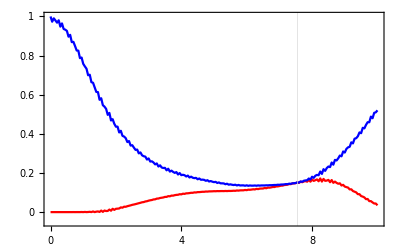

```mathematica
Show[ListPlot[{datIm,datIp},PlotStyle->{{Red},{Blue}},Joined->True,GridLines->{{7.55},{}},FrameTicks->{{{0,0.2,0.4,0.6,0.8,1},{None}},{{0,2,4,6,8,10},{None}}},GridLinesStyle->{{Black},{}},PlotLegends->Placed[{"",""},{0.2,0.85}],PlotRange->{{0,10},{-0.05,1}},Frame->True,LabelStyle->{18,Black}]]
```

```mathematica
r=50;
data=Import["Data/SupMat/survival_amplitude_Quench1_R20.dat"];
ampcomp=Table[data[[i,3]]+I*data[[i,4]],{i,1,Length[data]}];
datact=Table[{data[[i,1]],data[[i,2]],Log[Abs[ampcomp[[i]]]^2]},{i,1,Length[data]}];
data=Import["Data/SupMat/survival_probability_Quench1_R20.dat"];
datartct=Table[{data[[i,1]],-Log[Abs[data[[i,2]]]]/10},{i,1,Length[data]}];
datafz=Import["Data/SupMat/FisherZeros_Quench1_R20.dat"];
datafzo=Table[{datafz[[i,2]],datafz[[i,1]]},{i,1,Length[datafz]}];
```

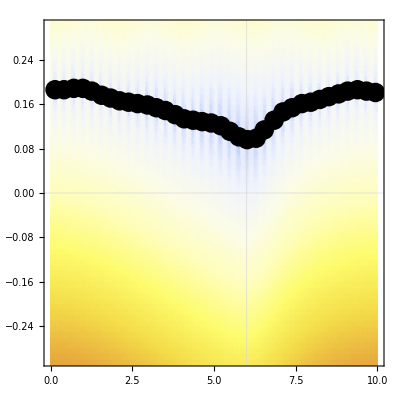

```mathematica
Show[ListDensityPlot[datact,GridLines->{{6},{0}},LabelStyle->{20,Black},GridLinesStyle->{{Black},{Dashed,Black,Thick}},PlotRange->{{0,10},{-0.3,0.3},{-20,20}},ColorFunction->"TemperatureMap"],ListPlot[datafzo,PlotStyle->{Black},PlotMarkers->{{"•",20}}]]
```

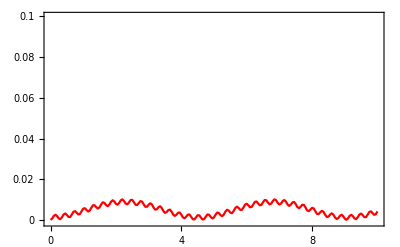

```mathematica
Show[ListPlot[{datartct},PlotStyle->{{Red,Thickness[0.004]},{Gray,Thickness[0.004]},{Gray,Thickness[0.004]}},Joined->True,GridLines->{{},{}},FrameTicks->{{{0,0.02,0.04,0.06,0.08,0.1},{None}},{{0,2,4,6,8,10},{None}}},GridLinesStyle->{{Black},{}},PlotRange->{{0,10},{-0.001,0.1}},Frame->True,LabelStyle->{18,Black}]]
```

### Bottom panel

```mathematica
(**** AQRM Hamiltonian ***)
g=3/4;
λ=0.0;
HAQRM[q_,p_,t_]=(p^2+q^2)/2-(1/2)*(1+(λ+2^(1/2)*g*q)^2)^(1/2);
```

```mathematica
Rr=1/50^(1/2);
Np=20;
Rd=0.0;
circ=Table[{Rr*Cos[2 π*i/Np],Rr*Sin[2 π*i/Np]},{i,1,Np}];
```

```mathematica
(*** Classical Phase space contours ***)
pin=0.75;
qin=0.0;
tf=8.25;
solt=NDSolve[{D[q[t],t]==D[HAQRM[q[t],p[t],t],p[t]],D[p[t],t]==-D[HAQRM[q[t],p[t],t],q[t]],q[0]==qin,p[0]==pin},{q,p},{t,0,tf}];
tintt=0.05;
qp3=Table[{q[t],p[t]}/. solt[[1]]/. t->i,{i,0,tf,tintt}];
```

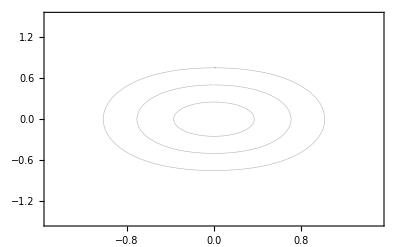

```mathematica
figsep=ListPlot[{qp,qp2,qp3},PlotStyle->Table[Directive[Black,Opacity[0.3],AbsoluteThickness[0.4]],{3}],Joined->True,Axes->False,Frame->True,PlotRange->{{-1.5,1.5},{-1.5,1.5}},LabelStyle->{16,Black}]
```

```mathematica
(*Importing data from Julia for Wigner function*)
datawigner=Import["Data/Wigner_quench0_t10.dat"];
```

```mathematica
(*Color for the Wigner function*)
FCo[t_]=Piecewise[{{ RGBColor[1,(2t)^3,(2t)^3],0<=t<=1/2},{ RGBColor[(1-2(t-1/2)),(1-2(t-1/2)),1],1/2<t<=1}}];
```

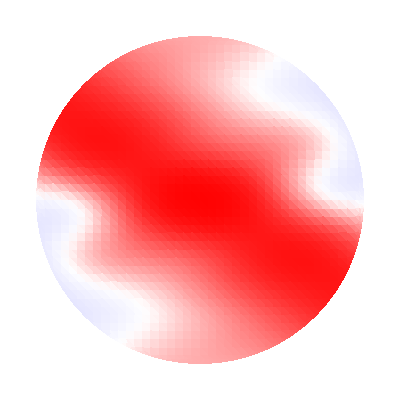

```mathematica
center={0,0};
circularPlot=ListDensityPlot[datawigner,RegionFunction->Function[{x,y,z},(x-center[[1]])^2+(y-center[[2]])^2<=Rr^2],PlotRange->{{center[[1]]-Rr,center[[1]]+Rr},{center[[2]]-Rr,center[[2]]+Rr},All},AspectRatio->1,Frame->False,Axes->False,ColorFunction->(FCo[1-fac*(#+0.35)]&),ColorFunctionScaling->False,PlotRangePadding->None,ImagePadding->0,Mesh->None,BoundaryStyle->None,Background->None]
```

```mathematica
fac=0.5/0.35;
wigner4=Show[ListDensityPlot[datawigner,PlotRange->{{-1.5,1.5},{-1.5,1.5},All},Frame->True,LabelStyle->{Black,16},ColorFunction->(FCo[1-fac*(#+0.35)]&),FrameTicks->{{{-1,0,1},None},{{-1,0,1},None}},ColorFunctionScaling->False,PlotLegends->False],figsep,ListPlot[circ,PlotStyle->Black]]
```

-Graphics-

```mathematica
Rr2=0.43;
Np=20;
Rd=0.0;
circ2=Table[{Rr2*Cos[2 π*i/Np],Rr2*Sin[2 π*i/Np]-1},{i,1,Np}];
wigner9z=Show[wigner9,Graphics[Inset[circularPlot,{0,-1},Center,Scaled[0.27]]],ListPlot[circ2,PlotStyle->Black],Graphics[{Thickness[0.001],Black,Line[{{-0.13,0},{-0.44,-1}}],Line[{{0.13,0},{0.44,-1}}]}]]
```

-Graphics-
-Graphics-

```mathematica
plots={{wigner0,wigner1,wigner2,wigner3,wigner4},{wigner5,wigner6z,wigner7z,wigner8z,wigner9z}};
nrows=Length[plots];
ncols=Length[plots[[1]]];
ticks={-1,0,1};
styledPlots=Table[Show[plots[[i,j]],Frame->True,Axes->False,FrameTicks->{{If[j==1,ticks,None],None},{If[i==nrows,ticks,None],None}}],{i,1,nrows},{j,1,ncols}];
GraphicsGrid[styledPlots,Spacings->{-60,-60}]
```

-Graphics-

```mathematica
cf=(FCo[1-fac*(#+0.35)]&);
vmin=-0.1;
vmax=0.1;   (*change to your real range*)
```

```mathematica
Legended[GraphicsGrid[styledPlots,Spacings->{-60.0,-60}],Placed[BarLegend[{cf,{vmin,vmax}},LegendLayout->"Row",(*makes it horizontal*)LegendMarkerSize->{300,20},LabelStyle->{14,Black}],Top]]
```

-Graphics-

## Figure 2

### (a-c)

```mathematica
r=10;
datanegt1=Import["Data/negativities_Quench1_kappa0_R50.dat"];
datRategt1=Table[{datanegt1[[i,1]],-(1/r)*Log[Abs[datanegt1[[i,6]]-datanegt1[[i,7]]]]},{i,1,Length[datanegt1]}] ;
datGgt1=Table[{datanegt1[[i,1]],-(1/r)*Log[Abs[1-datanegt1[[i,7]]/datanegt1[[i,6]]]]},{i,1,Length[datanegt1]}] ;
datneggt1=Table[{datanegt1[[i,1]],datanegt1[[i,2]]},{i,1,Length[datanegt1]}] ;
datWmingt1=Table[{datanegt1[[i,1]],Abs[datanegt1[[i,4]]]},{i,1,Length[datanegt1]}] ;
datanegt2=Import["Data/negativities_Quench1_kappa1_R50.dat"];
datRategt2=Table[{datanegt2[[i,1]],-(1/r)*Log[Abs[datanegt2[[i,6]]-datanegt2[[i,7]]]]},{i,1,Length[datanegt2]}] ;
datGgt2=Table[{datanegt2[[i,1]],-(1/r)*Log[Abs[1-datanegt2[[i,7]]/datanegt2[[i,6]]]]},{i,1,Length[datanegt2]}] ;
datneggt2=Table[{datanegt2[[i,1]],datanegt2[[i,2]]},{i,1,Length[datanegt2]}] ;
datWmingt2=Table[{datanegt2[[i,1]],Abs[datanegt2[[i,4]]]},{i,1,Length[datanegt2]}] ;
datanegt3=Import["Data/negativities_Quench1_kappa2_R50.dat"];
datRategt3=Table[{datanegt3[[i,1]],-(1/r)*Log[Abs[datanegt3[[i,6]]-datanegt3[[i,7]]]]},{i,1,Length[datanegt3]}] ;
datGgt3=Table[{datanegt3[[i,1]],-(1/r)*Log[Abs[1-datanegt3[[i,7]]/datanegt3[[i,6]]]]},{i,1,Length[datanegt3]}] ;
datneggt3=Table[{datanegt3[[i,1]],datanegt3[[i,2]]},{i,1,Length[datanegt3]}] ;
datWmingt3=Table[{datanegt3[[i,1]],Abs[datanegt3[[i,4]]]},{i,1,Length[datanegt3]}] ;
```

```mathematica
Show[ListPlot[datRategt1,PlotStyle->{Red},Joined->True,PlotLegends->Placed[{""},{0.1,0.9}],GridLines->{{7.55},{}},FrameTicks->{{{0,0.2,0.4,0.6,0.8,1,1.2,1.4},{None}},{{0,2,4,6,8,10},{None}}},GridLinesStyle->{{Black},{}},PlotRange->{{0,10},{-0.01,0.9}},Frame->True,LabelStyle->{18,Black}],ListPlot[datRategt2,Joined->True,PlotStyle->Blue,PlotLegends->Placed[{""},{0.1,0.75}]],ListPlot[datRategt3,Joined->True,PlotStyle->Gray,PlotLegends->Placed[{""},{0.1,0.58}]]]
```

-Graphics-

```mathematica
Show[ListPlot[datGgt1,PlotStyle->{Red},Joined->True,GridLines->{{7.55},{}},FrameTicks->{{{0,0.2,0.4,0.6,1.2,1.4},{None}},{{0,2,4,6,8,10},{None}}},GridLinesStyle->{{Black},{}},PlotRange->{{0,10},{-0.01,0.7}},Frame->True,LabelStyle->{18,Black}],ListPlot[datGgt2,Joined->True,PlotStyle->Blue],ListPlot[datGgt3,Joined->True,PlotStyle->Gray]]
```

-Graphics-

```mathematica
(*Importing data from Julia for Wigner function*)
datawigner=Import["../../src/output/wigner_rhot_data.dat"];
datwignorm=datawigner;
```

```mathematica
(*Color for the Wigner function*)
FCo[t_]=Piecewise[{{ RGBColor[1,(2t)^3,(2t)^3],0<=t<=1/2},{ RGBColor[(1-2(t-1/2)),(1-2(t-1/2)),1],1/2<t<=1}}];
```

```mathematica
Rr=1/50^(1/2);
Np=20;
Rd=0.0;
circ=Table[{Rr*Cos[2 π*i/Np],Rr*Sin[2 π*i/Np]},{i,1,Np}];
```

```mathematica
fac=0.5/0.35;
wignerfig=Show[ListDensityPlot[datwignorm,PlotRange->{{-1.2,1.2},{-1.2,1.2},All},Frame->True,FrameTicks->{{{-1,0,1},{}},{{-1,0,1},{}}},LabelStyle->{Black,22},GridLines->{{},{}},ColorFunction->(FCo[1-fac*(#+0.35)]&),ColorFunctionScaling->False(*,PlotLegends->Automatic*)],ListPlot[circ,PlotStyle->Black]]
```

-Graphics-

### (d)

```mathematica
DRt={{0.00075,2.76665597613699},{0.001,2.496059983783525},{0.0015,1.9456861919173398},{0.002,1.3791578414255383},{0.0025,0.877322722548429},{0.003,0.4623181557147887},{0.0035,0.20414523293650718},{0.004,0.11481134421425662}};
DGt={{0.00075,2.8431620455452533},{0.001,2.576527795404239},{0.0015,2.0341616072452955},{0.002,1.4763416774831415},{0.0025,0.9834865537338434},{0.003,0.5780913454378553},{0.0035,0.26030616669139955},{0.004,0.122313686294953616}};
```

```mathematica
logdataDRt=Log/@DRt;
logdataDGt=Log/@DGt;


qfit1=LinearModelFit[logdataDRt,{1,u,u^2,u^4},u];
qfit2=LinearModelFit[logdataDGt,{1,u,u^2,u^4},u];

qmodel1[x_]:=Exp[qfit1[Log[x]]];
qmodel2[x_]:=Exp[qfit2[Log[x]]];


Show[ListLogLogPlot[{DRt},PlotStyle->{Red,Darker[Green],Blue},PlotMarkers->{{"●",11},{"■",10},{"*",14}},Frame->True,PlotRange->{{0.0007,0.0049},{0.1,5}},PlotLegends->Placed[{""},{0.06,0.15}],LabelStyle->{Black,14}],ListLogLogPlot[{DGt},PlotStyle->{Darker[Green],Blue},PlotMarkers->{{"■",10},{"*",14}},PlotLegends->Placed[{""},{0.06,0.35}]],LogLogPlot[{qmodel1[x],qmodel2[x]},{x,Min[DRt[[All,1]]],Max[DGt[[All,1]]]},PlotStyle->{{Red,Dashed},{Darker[Green],Dashed},{Blue,Dashed}}]]
```

General::munfl: Exp[-728.171] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-892.317] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-728.171] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

-Graphics-

## TWA

### TWA

```mathematica
(*Initial Wigner function for TWA*)
q0=0.0;p0=0.0;
(*semiclassical parameter*)
r=50;
d[q_,p_]=Sqrt[(q-q0)^2+(p-p0)^2];
Wqp[q_,p_]= (2*r)/π Exp[-2*r*d[q,p]^2];
W[q_,p_]= Wqp[q,p];
```

```mathematica
(*Replicating initial state in the classical phase space*)
Δx=0.05;Δy=0.05; 
LX=15;LY=15; 
Qo=0;Po=0;
hps=Flatten[Table[{x,y},{x,Qo-LX,Qo+LX,Δx},{y,Po-LY,Po+LY,Δy}],1];
wliqp=Table[Wqp[hps[[k,1]],hps[[k,2]]],{k,1,Length[hps]}];
NR=10000; (*Number of points for TWA *)
ralqp=RandomChoice[wliqp->hps,NR];
```

General::munfl: Exp[-45000.] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-44850.2] is too small to represent as a normalized machine number; precision may be lost.

General::munfl: Exp[-44701.] is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

```mathematica
Show[DensityHistogram[ralqp,30,PlotRange->{{-1,1},{-1,1}},AxesLabel->{"x","p"}]]
```

-Graphics-

```mathematica
(*** Solving classical equations for motion for the TWA**)
ti=0;
tf=10.0;
dt=0.05;
g=5/4;(*coupling*)
λ=0.0;(*asymmetry bias*)
κ=0.05;(*Bosonic loss*)
HAQRM[q_,p_]=(p^2+q^2)/2-(1/2)*(1+(λ+2^(1/2)*g*q)^2)^(1/2);
eqsmov={};
eps=0.01;
Dq=(1/r)*κ/2;
Dp=(1/r)*κ/2;
Monitor[Do[
eqsmovinst={};
qin=ralqp[[k,1]];
pin=ralqp[[k,2]];
qq=qin;pp=pin;
data={{0,qq,pp}};
Do[ηq=RandomVariate[NormalDistribution[0,1]];
ηp=RandomVariate[NormalDistribution[0,1]];
pp=pp-(D[HAQRM[q,p],q]/.{q->qq,p->pp})* dt-dt*(κ/r^(1/2)) pp/2+Sqrt[Dp dt] ηp;
qq=qq+(D[HAQRM[q,p],p]/.{q->qq,p->pp})* dt-dt*(κ/r^(1/2)) qq/2+Sqrt[Dq dt] ηq;
AppendTo[data,{t+dt,qq,pp}],{t,0,tf-dt,dt}];
Do[qinst=data[[i,2]];
pinst=data[[i,3]];
AppendTo[eqsmovinst,{qinst,pinst}],{i,1,Length[data]}];
AppendTo[eqsmov,eqsmovinst],{k,1,Length[ralqp]}],N[k/Length[ralqp]]]
```

### Rate function

```mathematica
(*Importing exact survial amplitude from Julia*)
data=Import["Data/SupMat/survival_probability_Quench0_R50.dat"];
datasa=Import["../../../GrossPitaevskiiSCF/src/output/survivalamplitude.dat"];
```

```mathematica
SPb=Table[{(t-1)*dt,(2π )^1* Sum[Wqp[eqsmov[[k,t,1]],eqsmov[[k,t,2]]],{k,t,NR}]/(NR*2*r)},{t,1,201}];
dataRateTWA=Table[{SPb[[i,1]],-Log[Abs[SPb[[i,2]]]]/10},{i,1,Length[SPb]}];
```

```mathematica
dataRate=Table[{data[[i,1]],-Log[Abs[data[[i,2]]]]/10},{i,1,Length[data]}];
```

```mathematica
ampcomp=Table[datasa[[i,2]]+I*datasa[[i,3]],{i,1,Length[datasa]}];
dataRateEff=Table[{datasa[[i,1]],-Log[Abs[ampcomp[[i]]]^2]/10},{i,1,Length[ampcomp]}];
```

```mathematica
Show[ListPlot[dataRate,PlotRange->{{0,10},{-0.002,0.1}},Axes->False,PlotStyle->Red   ,Frame->True,Joined->True,LabelStyle->{16,Black},FrameLabel->{},GridLines->{{5},{}},PlotLegends->Placed[{""},{0.1,0.9}],GridLinesStyle->{{Black,Dashed},{Thick,Yellow,Dashed}}],ListPlot[dataRateEff,Joined->True,PlotStyle->{Blue},PlotLegends->Placed[{""},{0.1,0.75}]],ListPlot[dataRateTWA,Joined->True,PlotStyle->{Gray},PlotLegends->Placed[{""},{0.1,0.6}]]]
```

-Graphics-

```mathematica
r=10;
datanegt=Import["Data/negativities_Quench1_R50.dat"];
datGgt=Table[{datanegt[[i,1]],-(1/r)*Log[Abs[1-datanegt[[i,7]]/datanegt[[i,6]]]]},{i,1,Length[datanegt]}] ;
datanegteff=Import["../../../GrossPitaevskiiSCF/src/output/contributions.dat"];
datGgteff=Table[{datanegteff[[i,1]],-(1/r)*Log[Abs[1-Abs[datanegteff[[i,3]]/datanegteff[[i,2]]]]]},{i,1,Length[datanegteff]}] ;
```

```mathematica
Show[ListPlot[datGgt,PlotRange->{{0,10},{-0.02,0.8}},Axes->False,PlotStyle->Red   ,Frame->True,Joined->True,LabelStyle->{16,Black},FrameLabel->{},GridLines->{{7.55},{}},GridLinesStyle->{{Black},{Thick,Yellow,Dashed}}],ListPlot[datGgteff,Joined->True,PlotRange->All,PlotStyle->{Blue}],Plot[0,{x,0,10},PlotStyle->{Gray}],Plot[0,{x,0,10},PlotStyle->Gray]]
```

-Graphics-

```mathematica
Show[Plot[0,{x,0,10},PlotRange->{{0,10},{-0.02,1}},Axes->False,PlotStyle->Red   ,Frame->True,LabelStyle->{16,Black},FrameLabel->{},GridLines->{{5},{}},GridLinesStyle->{{Black,Dashed},{Thick,Yellow,Dashed}}],Plot[0,{x,0,10},PlotStyle->{Blue}],Plot[0,{x,0,10},PlotStyle->{Gray}]]
```

-Graphics-

### Histogram of Points for TWA

```mathematica
shot=152;
Listaqpt=Table[{eqsmov[[k,shot,1]],eqsmov[[k,shot,2]]},{k,1,Length[ralqp]}];
```

```mathematica
7.55/0.05
```

151.

```mathematica
Rr=1/50^(1/2);
Np=15;
Rd=0.0;
circ=Table[{Rr*Cos[2 π*i/Np],Rr*Sin[2 π*i/Np]},{i,1,Np}];
```

```mathematica
WignerTWAdata={};
CC={};
hs=0.05;
Do[
count=Length[Select[Listaqpt,i-hs/2<=#[[1]]<i+hs/2&&j-hs/2<=#[[2]]<j+hs/2&]];
AppendTo[WignerTWAdata,{i,j,count/(Length[Listaqpt]*hs*hs)}];
AppendTo[CC,{i,j,count}],{i,-1.2,1.2,hs},{j,-1.2,1.2,hs}];
```

```mathematica
Sum[WignerTWAdata[[i,3]]*hs^2,{i,1,Length[WignerTWA]}]
```

1.

```mathematica
dataSmooth=WignerTWAdata;
dataSmooth[[All,3]]=GaussianFilter[WignerTWAdata[[All,3]],1.2];
interp=Interpolation[dataSmooth,InterpolationOrder->1];
Show[DensityPlot[interp[q,p],{q,-1.2,1.2},{p,-1.2,1.2},PlotRange->{{-1.2,1.2},{-1.2,1.2},{0,1000}},Frame->True,FrameTicks->{{{-1,0,1},{}},{{-1,0,1},{}}},LabelStyle->{Black,22},ColorFunction->(Blend[{White,Lighter[Red,0.25]},#]&),ColorFunctionScaling->False,PlotLegends->False],ListPlot[circ,PlotStyle->Black]]
```

-Graphics-

```mathematica
smooth=SmoothKernelDistribution[Listaqpt,0.08];
Show[DensityPlot[PDF[smooth,{q,p}],{q,-1.2,1.2},{p,-1.2,1.2},PlotRange->All,PlotRangePadding->None,RegionFunction->Function[{q,p,z},-1.2<=q<=1.2&&-1.2<=p<=1.2],LabelStyle->{Black,35},FrameTicks->{{{-1,0,1},{}},{{-1,0,1},{}}},ColorFunction->(Blend[{White,Lighter[Red,0.3]},#]&),ColorFunctionScaling->True,PlotPoints->80,MaxRecursion->3,Frame->True,Background->White,ImageSize->Large],ListPlot[circ,PlotStyle->Black]]
```

-Graphics-

### Exact Wigner function

```mathematica
(*Importing data from Julia for Wigner function*)
datawigner=Import["../../src/output/wigner_rhot_data.dat"];
datwignorm=Table[{datawigner[[i,1]],datawigner[[i,2]],datawigner[[i,3]]},{i,1,Length[datawigner]}];
```

```mathematica
(*Color for the Wigner function*)
FCo[t_]=Piecewise[{{ RGBColor[1,(2t)^3,(2t)^3],0<=t<=1/2},{ RGBColor[(1-2(t-1/2)),(1-2(t-1/2)),1],1/2<t<=1}}];
```

```mathematica
Rr=1/50^(1/2);
Np=20;
Rd=0.0;
circ=Table[{Rr*Cos[2 π*i/Np],Rr*Sin[2 π*i/Np]},{i,1,Np}];
```

```mathematica
(*** Classical Phase space contours ***)
pin=0.8;
qin=0.0;
tf=100;
solt=NDSolve[{D[q[t],t]==D[HAQRM[q[t],p[t],t],p[t]],D[p[t],t]==-D[HAQRM[q[t],p[t],t],q[t]],q[0]==qin,p[0]==pin},{q,p},{t,0,tf}];
tintt=0.01;
qp3=Table[{q[t],p[t]}/. solt[[1]]/. t->i,{i,0,tf,tintt}];
```

```mathematica
figsep=ListPlot[{qp,qp2,qp3},PlotStyle->{Black},Axes
->False,Frame->True,PlotRange->{{-2.5,2.5},{-2.5,2.5}},LabelStyle->{16,Black}]
```

-Graphics-

```mathematica
fac=0.5/0.35;
wigner2=Show[ListDensityPlot[datwignorm,PlotRange->{{-1.2,1.2},{-1.2,1.2},All},Frame->True,LabelStyle->{Black,22},FrameTicks->{{{-1,0,1},{}},{{-1,0,1},{}}},ColorFunction->(FCo[1-fac*(#+0.35)]&),ColorFunctionScaling->False(*,PlotLegends->Automatic*)],ListPlot[circ,PlotStyle->Black]]
```

-Graphics-